```mathematica
(*We will start with gaussian*)
ClearAll[GenerateTurbulenceCore,GaussianMarketAdapter];
Options[GenerateTurbulenceCore]={"RandomMethod"->"MersenneTwister"};
GenerateTurbulenceCore[seed_Integer,length_Integer?Positive,OptionsPattern[]]:=Module[{method,signal},method=OptionValue["RandomMethod"];
signal=BlockRandom[SeedRandom[seed,Method->method];
RandomVariate[NormalDistribution[0.,1.],length]];
<|"Model"->"GaussianReference","Seed"->seed,"Length"->length,(*Domain-neutral Gaussian signal*)"Signal"->signal,"Innovations"->signal,(*Derived measurement,not a dynamical process*)"Activity"->signal^2,(*Constant by definition in this reference model*)"ConditionalScale"->ConstantArray[1.,length],"Parameters"-><|"Distribution"->"NormalDistribution[0,1]","Independent"->True,"RandomMethod"->method|>|>];
```

```mathematica
(*Market adapter*)
Options[GaussianMarketAdapter]={"InitialPrice"->100.,"AnnualizedLogDrift"->0.,"AnnualizedVolatility"->0.20,"PeriodsPerYear"->252};
GaussianMarketAdapter[core_Association,OptionsPattern[]]:=Module[{initialPrice,annualizedLogDrift,annualizedVolatility,periodsPerYear,periodDrift,periodScale,returns,prices},initialPrice=N@OptionValue["InitialPrice"];
annualizedLogDrift=N@OptionValue["AnnualizedLogDrift"];
annualizedVolatility=N@OptionValue["AnnualizedVolatility"];
periodsPerYear=OptionValue["PeriodsPerYear"];
periodDrift=annualizedLogDrift/periodsPerYear;
periodScale=annualizedVolatility/Sqrt[periodsPerYear];
(*No sample centering or sample rescaling*)returns=periodDrift+periodScale core["Signal"];
prices=Exp[Log[initialPrice]+Accumulate[returns]];
Join[core,<|"Adapter"->"Market","Returns"->returns,"Prices"->prices,(*Flat theoretical conditional volatility*)"Volatility"->ConstantArray[periodScale,Length[returns]],"RelativeVolatility"->ConstantArray[1.,Length[returns]],"MarketParameters"-><|"InitialPrice"->initialPrice,"AnnualizedLogDrift"->annualizedLogDrift,"AnnualizedVolatility"->annualizedVolatility,"PeriodsPerYear"->periodsPerYear,"PeriodScale"->periodScale|>|>]];
```

```mathematica
gaussianCore=GenerateTurbulenceCore[20260817,8192];
gaussianResult=GaussianMarketAdapter[gaussianCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];


(*Now adding a higher number of peaks to the original distribution*)
ClearAll[AddIndependentPeakFrequency];
Options[AddIndependentPeakFrequency]={"PeakProbability"->0.02,"PeakAmplification"->3.,"EventSeed"->20260818,"RandomMethod"->"MersenneTwister"};
AddIndependentPeakFrequency[baseCore_Association,OptionsPattern[]]:=Module[{peakProbability,peakAmplification,eventSeed,randomMethod,length,peakIndicator,varianceNormalization,activityMultiplier,peakSignal},peakProbability=OptionValue["PeakProbability"];
peakAmplification=N@OptionValue["PeakAmplification"];
eventSeed=OptionValue["EventSeed"];
randomMethod=OptionValue["RandomMethod"];
length=baseCore["Length"];
peakIndicator=BlockRandom[SeedRandom[eventSeed,Method->randomMethod];
RandomVariate[BernoulliDistribution[peakProbability],length]];
(*E[activityMultiplier^2]=1. This preserves the theoretical unconditional variance without centering or normalizing the generated sample.*)varianceNormalization=Sqrt[(1.-peakProbability)+peakProbability peakAmplification^2];
activityMultiplier=(1.+(peakAmplification-1.) peakIndicator)/varianceNormalization;
peakSignal=activityMultiplier baseCore["Signal"];
Join[baseCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"IndependentPeakFrequency","Version"->"0.2","ParentStage"->"GaussianBase","GaussianSource"->baseCore["Signal"],"Signal"->peakSignal,"Activity"->peakSignal^2,"PeakIndicator"->peakIndicator,"ConditionalScale"->activityMultiplier,"Parameters"->Join[baseCore["Parameters"],<|"PeakProbability"->peakProbability,"PeakAmplification"->peakAmplification,"EventSeed"->eventSeed,"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];

(*New Stage using separate variables*)
peakFrequencyProbability=0.02;
peakFrequencyAmplification=3.;
peakFrequencyEventSeed=20260818;
peakFrequencyCore=AddIndependentPeakFrequency[gaussianCore,"PeakProbability"->peakFrequencyProbability,"PeakAmplification"->peakFrequencyAmplification,"EventSeed"->peakFrequencyEventSeed];
```

```mathematica
(*Market adapter for a higher number of peaks*)
peakFrequencyMarketBase=GaussianMarketAdapter[peakFrequencyCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
peakFrequencyRelativeScale=peakFrequencyCore["ConditionalScale"];
peakFrequencyPeriodScale=peakFrequencyMarketBase["MarketParameters"]["PeriodScale"];
peakFrequencyResult=Join[peakFrequencyMarketBase,<|"Volatility"->peakFrequencyPeriodScale peakFrequencyRelativeScale,"RelativeVolatility"->peakFrequencyRelativeScale|>];
```

```mathematica
(*Construction Summary so far*)
peakFrequencyConstructionSummary=<|"Observations"->peakFrequencyCore["Length"],"ExpectedPeakCount"->peakFrequencyProbability peakFrequencyCore["Length"],"RealizedPeakCount"->Total[peakFrequencyCore["PeakIndicator"]],"RealizedPeakFrequency"->Mean[peakFrequencyCore["PeakIndicator"]],"PeakAmplification"->peakFrequencyAmplification,"TheoreticalSignalVariance"->peakFrequencyCore["Parameters"]["TheoreticalSignalVariance"]|>;
Dataset[peakFrequencyConstructionSummary]
```

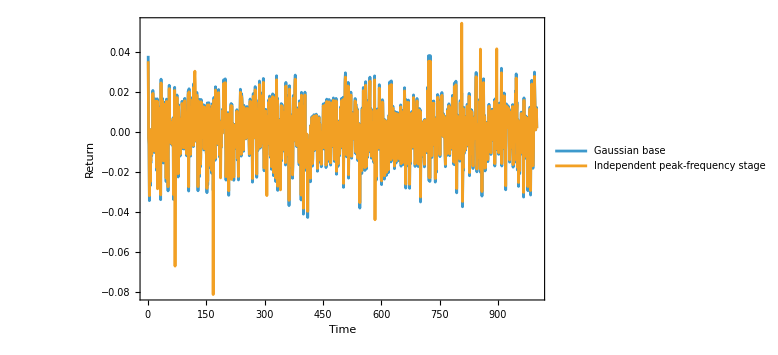

```mathematica
(*Visual Comparison with original and a higher number of peak frequency*)
peakFrequencyComparisonPlot=ListLinePlot[{Take[gaussianResult["Returns"],1000],Take[peakFrequencyResult["Returns"],1000]},PlotLegends->{"Gaussian base","Independent peak-frequency stage"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
peakFrequencyComparisonPlot
```

```mathematica
(*Adding a proper distributino for peak severity*)
ClearAll[AddPeakSeverityDistribution];
Options[AddPeakSeverityDistribution]={"SeverityLogMean"->0.44,"SeverityLogStandardDeviation"->0.55,"SeveritySeed"->20260819,"RandomMethod"->"MersenneTwister"};
AddPeakSeverityDistribution[peakCore_Association,OptionsPattern[]]:=Module[{severityLogMean,severityLogStandardDeviation,severitySeed,randomMethod,length,peakProbability,peakIndicator,gaussianSource,severityExcess,severityMultiplier,meanSeverityExcess,secondMomentSeverityExcess,eventSeveritySecondMoment,varianceNormalization,relativeActivityScale,severitySignal},severityLogMean=N@OptionValue["SeverityLogMean"];
severityLogStandardDeviation=N@OptionValue["SeverityLogStandardDeviation"];
severitySeed=OptionValue["SeveritySeed"];
randomMethod=OptionValue["RandomMethod"];
length=peakCore["Length"];
peakProbability=peakCore["Parameters"]["PeakProbability"];
peakIndicator=peakCore["PeakIndicator"];
gaussianSource=peakCore["GaussianSource"];
(*Positive excess severity.At a peak:multiplier=1+LogNormal draw Outside a peak:multiplier=1*)severityExcess=BlockRandom[SeedRandom[severitySeed,Method->randomMethod];
RandomVariate[LogNormalDistribution[severityLogMean,severityLogStandardDeviation],length]];
severityMultiplier=1.+peakIndicator severityExcess;
(*Analytical moments of Y~LogNormalDistribution[mu,sigma]*)meanSeverityExcess=Exp[severityLogMean+severityLogStandardDeviation^2/2.];
secondMomentSeverityExcess=Exp[2. severityLogMean+2. severityLogStandardDeviation^2];
(*M=1+Y during an event*)eventSeveritySecondMoment=1.+2. meanSeverityExcess+secondMomentSeverityExcess;
(*Preserve E[Signal^2]=1 theoretically.This is model-level normalization,not normalization of the realized sample.*)varianceNormalization=Sqrt[(1.-peakProbability)+peakProbability eventSeveritySecondMoment];
relativeActivityScale=severityMultiplier/varianceNormalization;
severitySignal=relativeActivityScale gaussianSource;
Join[peakCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"PeakSeverityDistribution","Version"->"0.3","ParentStage"->"IndependentPeakFrequency","Signal"->severitySignal,"Activity"->severitySignal^2,"PeakSeverityExcess"->severityExcess,"PeakSeverityMultiplier"->severityMultiplier,"ConditionalScale"->relativeActivityScale,"Parameters"->Join[peakCore["Parameters"],<|"SeverityDistribution"->"1 + LogNormalDistribution[mu,sigma]","SeverityLogMean"->severityLogMean,"SeverityLogStandardDeviation"->severityLogStandardDeviation,"SeveritySeed"->severitySeed,"ExpectedEventSeverity"->1.+meanSeverityExcess,"ExpectedEventSeverityRMS"->Sqrt[eventSeveritySecondMoment],"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];
peakSeverityLogMean=0.44;
peakSeverityLogStandardDeviation=0.55;
peakSeveritySeed=20260819;
peakSeverityCore=AddPeakSeverityDistribution[peakFrequencyCore,"SeverityLogMean"->peakSeverityLogMean,"SeverityLogStandardDeviation"->peakSeverityLogStandardDeviation,"SeveritySeed"->peakSeveritySeed];
peakSeverityMarketBase=GaussianMarketAdapter[peakSeverityCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
peakSeverityRelativeScale=peakSeverityCore["ConditionalScale"];
peakSeverityPeriodScale=peakSeverityMarketBase["MarketParameters"]["PeriodScale"];
peakSeverityResult=Join[peakSeverityMarketBase,<|"Volatility"->peakSeverityPeriodScale peakSeverityRelativeScale,"RelativeVolatility"->peakSeverityRelativeScale|>];
```

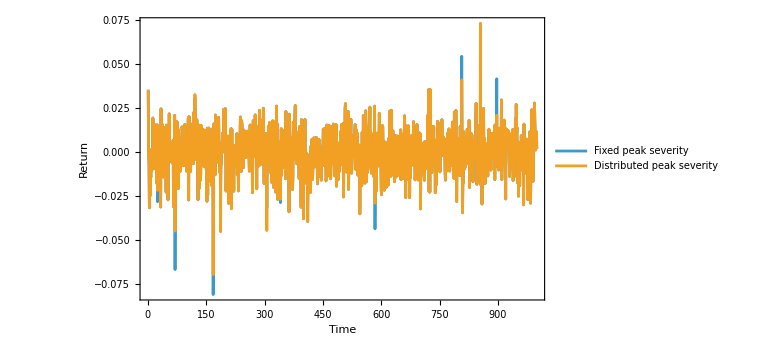

```mathematica
(*Visual Comparison*)
peakSeverityComparisonPlot=ListLinePlot[{Take[peakFrequencyResult["Returns"],1000],Take[peakSeverityResult["Returns"],1000]},PlotLegends->{"Fixed peak severity","Distributed peak severity"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
peakSeverityComparisonPlot
```

```mathematica
(*Now adding persistence*)
ClearAll[AddPersistentPeakEpisodes];
Options[AddPersistentPeakEpisodes]={"Persistence"->0.85};
AddPersistentPeakEpisodes[severityCore_Association,OptionsPattern[]]:=Module[{persistence,peakProbability,severityLogMean,severityLogStandardDeviation,peakIndicator,severityExcess,gaussianSource,peakImpulse,meanSeverityExcess,secondMomentSeverityExcess,meanImpulse,varianceImpulse,stationaryMeanActivity,stationaryVarianceActivity,stationarySecondMomentActivity,varianceNormalization,initialActivity,persistentActivity,relativeActivityScale,persistentSignal,activityHalfLife},persistence=N@OptionValue["Persistence"];
If[persistence<0.||persistence>=1.,Return[Failure["InvalidPersistence",<|"Message"->"Persistence must satisfy 0 <= rho < 1."|>]]];
peakProbability=severityCore["Parameters"]["PeakProbability"];
severityLogMean=severityCore["Parameters"]["SeverityLogMean"];
severityLogStandardDeviation=severityCore["Parameters"]["SeverityLogStandardDeviation"];
peakIndicator=severityCore["PeakIndicator"];
severityExcess=severityCore["PeakSeverityExcess"];
gaussianSource=severityCore["GaussianSource"];
(*Existing event times and severities are reused.No new random values are introduced.*)peakImpulse=peakIndicator severityExcess;
meanSeverityExcess=Exp[severityLogMean+severityLogStandardDeviation^2/2.];
secondMomentSeverityExcess=Exp[2. severityLogMean+2. severityLogStandardDeviation^2];
meanImpulse=peakProbability meanSeverityExcess;
varianceImpulse=peakProbability secondMomentSeverityExcess-meanImpulse^2;
(*Stationary moments of:H[t]=persistence H[t-1]+impulse[t]*)stationaryMeanActivity=meanImpulse/(1.-persistence);
stationaryVarianceActivity=varianceImpulse/(1.-persistence^2);
stationarySecondMomentActivity=stationaryVarianceActivity+stationaryMeanActivity^2;
(*Preserve theoretical E[Signal^2]=1.*)varianceNormalization=Sqrt[1.+2. stationaryMeanActivity+stationarySecondMomentActivity];
(*Start at the stationary mean to reduce startup transients.*)initialActivity=stationaryMeanActivity;
persistentActivity=Rest@FoldList[persistence #1+#2&,initialActivity,peakImpulse];
relativeActivityScale=(1.+persistentActivity)/varianceNormalization;
persistentSignal=relativeActivityScale gaussianSource;
activityHalfLife=If[persistence==0.,0.,Log[0.5]/Log[persistence]];
Join[severityCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"PersistentPeakEpisodes","Version"->"0.4","ParentStage"->"PeakSeverityDistribution","Signal"->persistentSignal,"Activity"->persistentSignal^2,"PeakImpulse"->peakImpulse,"PersistentActivity"->persistentActivity,"ConditionalScale"->relativeActivityScale,"Parameters"->Join[severityCore["Parameters"],<|"Persistence"->persistence,"ActivityHalfLife"->activityHalfLife,"StationaryMeanActivity"->stationaryMeanActivity,"StationaryVarianceActivity"->stationaryVarianceActivity,"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];
persistentClusterCoefficient=0.85;
persistentClusterCore=AddPersistentPeakEpisodes[peakSeverityCore,"Persistence"->persistentClusterCoefficient];
```

```mathematica
(*Market adapter*)
persistentClusterMarketBase=GaussianMarketAdapter[persistentClusterCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
persistentClusterRelativeScale=persistentClusterCore["ConditionalScale"];
persistentClusterPeriodScale=persistentClusterMarketBase["MarketParameters"]["PeriodScale"];
persistentClusterResult=Join[persistentClusterMarketBase,<|"Volatility"->persistentClusterPeriodScale*persistentClusterRelativeScale,"RelativeVolatility"->persistentClusterRelativeScale|>];
```